### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/FluctuatingTemperature

### Keywords

Details

# Fluctuating Environment

This trait-based model considers competition in a variable environment, where an environmental factor such as temperature varies periodically.  Species have a unimodal growth response to temperature, with the optimal temperature, Topt, as an evolvable trait.

```mathematica
Needs["EcoEvo`"]
```

EcoEvo Package Version 0.9.0α (May 14, 2018)

Set up model.

```mathematica
SetModel[{
Guild[1]->{Variable->n,Equation->dn,Trait[1]->{Variable->Topt}},Period:>τ
}];

dn[i_]:=( μ E^(-(Subscript[Topt, i]-T[t])^2/σ^2)(1-Sum[Subscript[n, j][t],{j,Nsp[1]}])-d)*Subscript[n, i][t];
T[t]:=15+6 Sin[2π/τ t]; (* temperature *)

τ=365; (* period *)
σ=2.5; (* width of temperature-response curve *)
μ=3.0; (* maximum growth rate *)
d=0.1; (* death rate *)
```

Plot temperature vs time over one period.

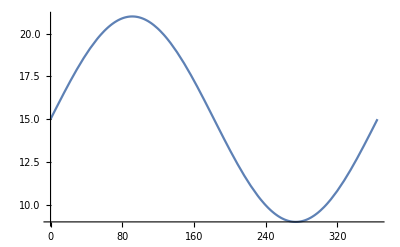

```mathematica
Plot[T[t],{t,0,τ}]
```

Plot invasion rate in the empty environment.

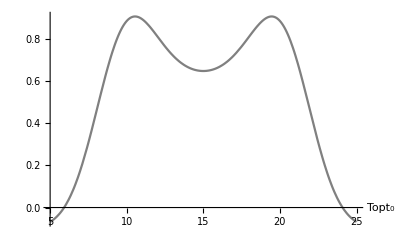

```mathematica
PlotInv[{Subscript[Topt, 0],5,25}]
```

Looks like the underlying fitness landscape is bimodal (due to the sinusoidal forcing).  Let's find (at least one of) the maxima.

```mathematica
MaximizeInv[]
```

{0.904409,{Topt_0→10.5427}}

Now let's simulate the model with a species whose optimum matches the environmental mean.

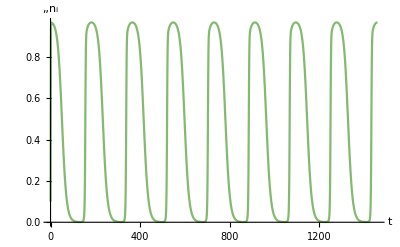

```mathematica
sol=EcoSim[{Subscript[Topt, 1]->15},{Subscript[n, 1]->0.1},4τ];
PlotDynamics[sol]
```

Use the final value as an initial guess to find the limit cycle.

```mathematica
eq=FindEcoCycle[{Subscript[Topt, 1]->15},FinalSlice[sol]]
```

{n_1→InterpolatingFunction[…]}

Now plot the invasion fitness landscape.

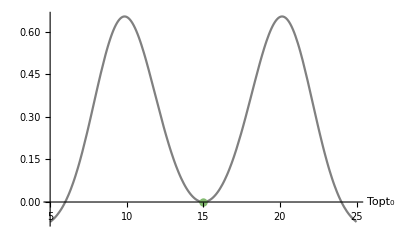

```mathematica
PlotInv[{Subscript[Topt, 1]->15},eq,{Subscript[Topt, 0],5,25}]
```

Looks like a non-ESS at Topt=15.  Let's verify with a PIP.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {Topt_1→17.1429}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {Topt_1→17.3571}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {Topt_1→9.24107}. Trying EcoSim.

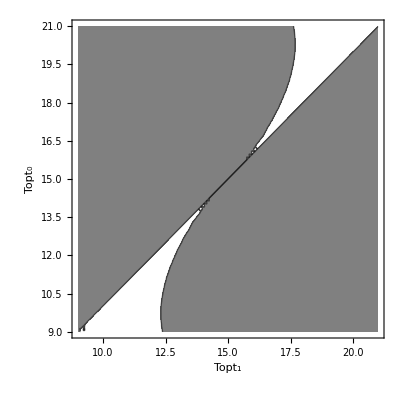

```mathematica
PlotPIP[{Subscript[Topt, 1],9,21},FindEcoAttractorOpts->{TestStability->False},Monitor->True]
```

Looks to be both convergence stable and non-ESS — an evolutionary branching point.  We can simulate the eco-evolutionary dynamics of branching, using a small trait variance to approximate Adaptive Dynamics' separation of time scales.

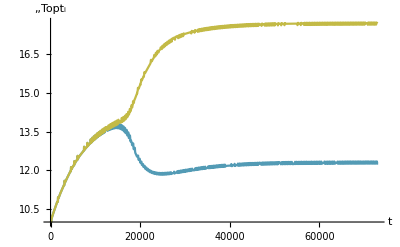

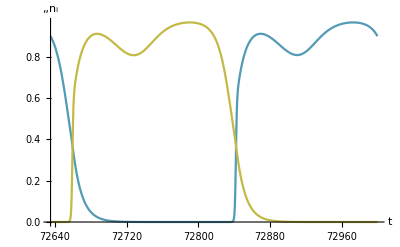

```mathematica
sol=EcoEvoSim[{Subscript[Topt, 1]->10,Subscript[Topt, 2]->10.0001},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{V[Topt]->0.01},200τ];
PlotDynamics[sol,Topt]
PlotDynamics[FinalSlice[sol,τ],n]
```

We can use the final values of this EcoEvoSim as an initial guess for FindEcoCycleEvoEq.

```mathematica
eq2=FindEcoCycleEvoEq[FinalSlice[sol],{V[Topt]->10},Method->"FixedPoint"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {208.158}. NIntegrate obtained -0.00790478 and 2.1688×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {208.158}. NIntegrate obtained 0.00140017 and 2.20148×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {24.9455}. NIntegrate obtained 0.0166892 and 2.39474×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{n_1→InterpolatingFunction[…],n_2→InterpolatingFunction[…],Topt_1→12.3115,Topt_2→17.6886}

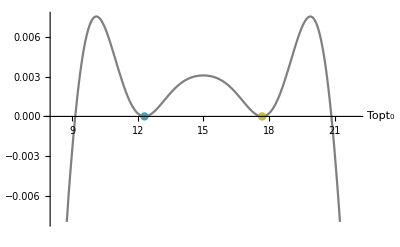

```mathematica
PlotInv[eq2,{Subscript[Topt, 0],8,22}]
```

Not an ESS yet — let's slip in a third species at Topt=15 and follow the eco-evolutionary dynamics.

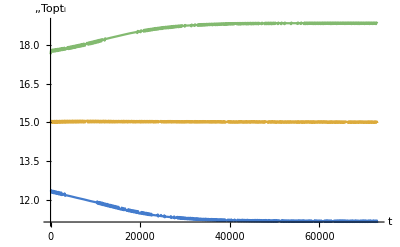

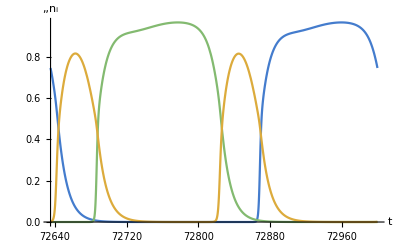

```mathematica
sol=EcoEvoSim[Join[FinalSlice[eq2],{Subscript[Topt, 3]->15,Subscript[n, 3]->0.1}],{V[Topt]->0.01},200τ];
PlotDynamics[sol,Topt]
PlotDynamics[FinalSlice[sol,τ],n]
```

```mathematica
FinalSlice[sol]
```

{n_1→0.745988,n_2→1.83784×10^-8,n_3→0.00156246,Topt_1→11.1507,Topt_2→18.8487,Topt_3→14.9757}

We can again use the final values as initial guesses for FindEcoCycleEvoEq.  We fix the center species at Topt=15 using Fixed, which makes it easier to find the ESS.

```mathematica
eq3=FindEcoCycleEvoEq[{Subscript[n, 1]->0.75,Subscript[n, 2]->2*^-8,Subscript[n, 3]->0.0016,Subscript[Topt, 1]->11.15,Subscript[Topt, 2]->18.85},Fixed->{Subscript[Topt, 3]->15}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {231.684}. NIntegrate obtained -0.0100012 and 1.44689×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {231.684}. NIntegrate obtained -0.00674612 and 1.45631×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {48.4709}. NIntegrate obtained -0.0752454 and 1.60201×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.41975, step size is effectively zero; singularity or stiff system suspected.

{n_1→InterpolatingFunction[…],n_2→InterpolatingFunction[…],n_3→InterpolatingFunction[…],Topt_1→11.1812,Topt_2→18.8188,Topt_3→15}

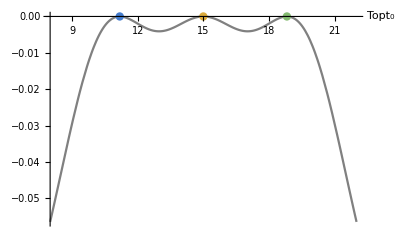

```mathematica
PlotInv[eq3,{Subscript[Topt, 0],8,22}]
```

Finally a global ESS:

```mathematica
GlobalESSQ[eq3]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.35886}. NIntegrate obtained -0.13519 and 0.000027677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.35886}. NIntegrate obtained -0.0248536 and 0.0000309148 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{True},{{-3.48941×10^-6,{Topt→15.}}}}

The three-species ESS is robust to a little within-species trait variation, but too much results in convergence on a two-species ESS.

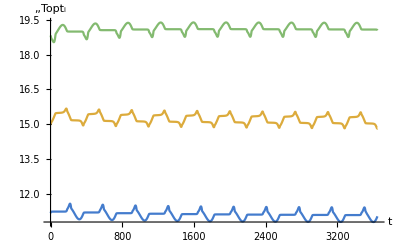

```mathematica
sol=EcoEvoSim[FinalSlice[eq3],{V[Topt]->0.1},10τ];
PlotDynamics[sol,Topt]
```

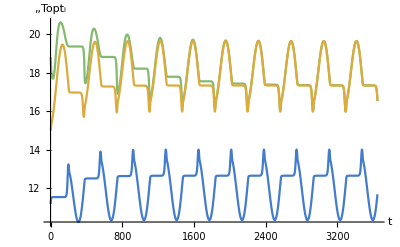

```mathematica
sol=EcoEvoSim[FinalSlice[eq3],{V[Topt]->0.5},10τ];
PlotDynamics[sol,Topt]
```

### References

Kremer CT, Klausmeier CA. 2017. Species packing in eco-evolutionary models of seasonally fluctuating environments. Ecology Letters 20: 1158–1168

More About

Related Tutorials

Related Wolfram Education Group Courses